```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\Integrate\\Программа\\Integrate"];
```

Тест 1

Import::nffil: File test1.txt not found during Import.

ListLinePlot::lpn: Transpose[$Failed] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Transpose[$Failed],GridLines→Automatic],].

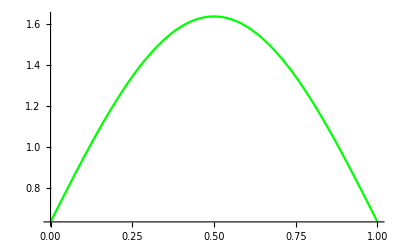
Show[ListLinePlot[Transpose[$Failed],GridLines→Automatic],-Graphics-]

```mathematica
data=Import["test1.txt","Table"];
(*Точное решение*)
u=Sin[π x]+2/π;
Show[ListLinePlot[Transpose@data,GridLines->Automatic],Plot[u,{x,0,1},PlotStyle->Green]]
```

Тест 2

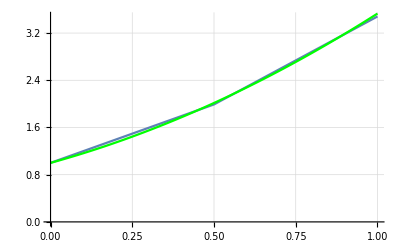

```mathematica
data=Import["test2.txt","Table"];
(*Точное решение*)
u=1+x^2+(2x)/(2-Log[2]);
Show[ListLinePlot[Transpose@data,GridLines->Automatic],Plot[u,{x,0,1},PlotStyle->Green]]
```

```mathematica
x^3-4Integrate[x^2 ⅇ^(x^2 s^4)s^3,{s,0,1}]==x^3-(ⅇ^(x^2)-1)//FullSimplify
```

True

```mathematica
NMaximize[1/(2π)Integrate[Abs[s Sin[x]],{s,0,π},Assumptions->{x>=0,x<=π}],{x,0,π}]
```

{0.785398,{x→1.5708}}

```mathematica
π/4//N
```

0.785398

```mathematica
Table[{{N@((π/4)^i)2/π}},{i,1,12}]//TableForm
```

0.5
0.392699
0.308425
0.242237
0.190252
0.149424
0.117357
0.092172
0.0723917
0.0568563
0.0446549
0.0350719

Тест 1 из методички с первыми начальными условиями

Метод квадратур

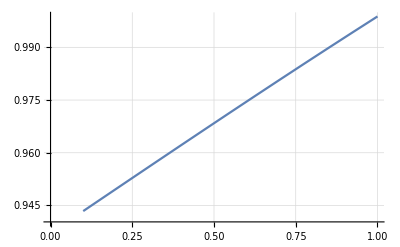

```mathematica
data=Import["task1.txt","Table"];
ListLinePlot[Transpose@data,GridLines->Automatic]
```

Метод простой итерации

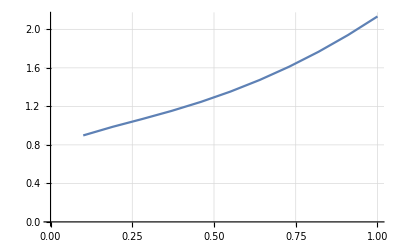

```mathematica
data=Import["task1.txt","Table"];
ListLinePlot[Transpose@data,GridLines->Automatic]
```

Вторая правая часть x^2+√x

Метод квадратур

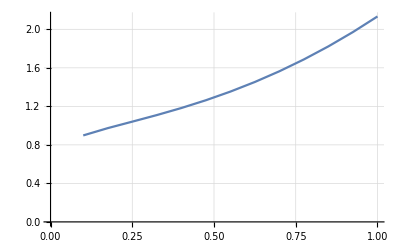

```mathematica
data=Import["task1.txt","Table"];
ListLinePlot[Transpose@data,GridLines->Automatic]
```

```mathematica
data=Import["task1.txt","Table"];
ListLinePlot[Transpose@data,GridLines->Automatic]
```

-Graphics-

Метод простой итерации

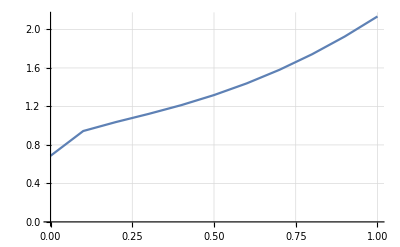

```mathematica
data=Import["task1.txt","Table"];
ListLinePlot[Transpose@data,GridLines->Automatic]
```

```mathematica
data=Import["task1.txt","Table"];
ListLinePlot[Transpose@data,GridLines->Automatic]
```

-Graphics-

### Сингулярные уравнения

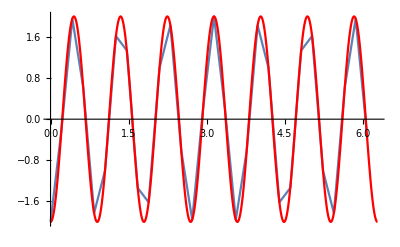

```mathematica
data=Import["singular.txt", "Table"];
Show[ListLinePlot[Transpose@data,PlotRange->{{0,2π},{-2,2}}],Plot[-2Cos[7ϕ],{ϕ,0,2π},PlotStyle->Red]]
```

```mathematica
Integrate[Cos[(ϕ1+ϕ)/2]/Sin[(ϕ1-ϕ)/2](-2Cos[ϕ]),{ϕ,0,2π},Assumptions->{ϕ1>0,ϕ1<2π},PrincipalValue->True]
```

ConditionalExpression[-2 ⅈ ⅇ^(-2 ⅈ ϕ1) π, ϕ1≤π]

```mathematica
Integrate[Sin[(ϕ1+ϕ)/2]/Sin[(ϕ1-ϕ)/2](-2Cos[ϕ]),{ϕ,0,2π},Assumptions->{ϕ1>0,ϕ1<2π},PrincipalValue->True]
```

-4 π Sin[ϕ1]^2

```mathematica
ExpToTrig[-2 ⅈ ⅇ^(-2 ⅈ ϕ1) π]
```

-2 ⅈ π Cos[2 ϕ1]-2 π Sin[2 ϕ1]

```mathematica
-4 π Sin[ϕ1]^2+(2 ⅈ π Cos[2 ϕ1]-2 π Sin[2 ϕ1])//FullSimplify
```

2 π (-1+(1+ⅈ) Cos[2 ϕ1]-Sin[2 ϕ1])

```mathematica
(*Q*)
1/(2π)*1/((x-ξ)^2+(y-η)^2){-(y-η),x-ξ}
```

{(-y+η)/(2 π ((y-η)^2+(x-ξ)^2)),(x-ξ)/(2 π ((y-η)^2+(x-ξ)^2))}

```mathematica
{x,y}.%
```

(x (-y+η))/(2 π ((y-η)^2+(x-ξ)^2))+(y (x-ξ))/(2 π ((y-η)^2+(x-ξ)^2))

```mathematica
expr=FullSimplify[%/.{x->Cos[ϕ1],y->Sin[ϕ1],ξ->Cos[ϕ],η->Sin[ϕ]},Assumptions->{ϕ>=0,ϕ<=2π,ϕ1>=0,ϕ1<=2π}]
```

Cot[(ϕ-ϕ1)/2]/(4 π)

```mathematica
Integrate[expr*(-2Cos[ϕ]),{ϕ,0,2π},PrincipalValue->True,Assumptions->{ϕ1>=0,ϕ1<=2π}]
```

ConditionalExpression[ⅈ Cos[ϕ1]+Sin[ϕ1], ϕ1≤π]

```mathematica
Integrate[expr*(-2Cos[4ϕ]),{ϕ,0,2π},PrincipalValue->True,Assumptions->{ϕ1>=0,ϕ1<=2π}]
```

ConditionalExpression[ⅈ ⅇ^(-4 ⅈ ϕ1), ϕ1≤π]

```mathematica
ExpToTrig[ⅈ ⅇ^(-4 ⅈ ϕ1)]
```

ⅈ Cos[4 ϕ1]+Sin[4 ϕ1]

```mathematica
Integrate[expr*(-2Cos[4ϕ]),{ϕ,0,2π},PrincipalValue->True,Assumptions->{ϕ1>=-π,ϕ1<=π}]
```

ConditionalExpression[Sin[4 ϕ1], ϕ1≥0]

```mathematica
Ch[n_,x_] = ChebyshevT[n,x];
```

```mathematica
Series[x^2 Exp[x^2 s^2],{x,s,10}]
```

ⅇ^(s^4) s^2+2 ⅇ^(s^4) (s+s^5) (x-s)+ⅇ^(s^4) (1+5 s^4+2 s^8) (x-s)^2+2/3 ⅇ^(s^4) s^3 (6+9 s^4+2 s^8) (x-s)^3+1/6 ⅇ^(s^4) s^2 (6+39 s^4+4 s^8 (7+s^4)) (x-s)^4+1/15 ⅇ^(s^4) s^5 (45+95 s^4+40 s^8+4 s^12) (x-s)^5+1/90 ⅇ^(s^4) s^4 (45+375 s^4+390 s^8+108 s^12+8 s^16) (x-s)^6+1/315 ⅇ^(s^4) s^7 (420+1155 s^4+714 s^8+140 s^12+8 s^16) (x-s)^7+(ⅇ^(s^4) s^6 (420+4305 s^4+8 s^8 (735+301 s^4+44 s^8+2 s^12)) (x-s)^8)/2520+(ⅇ^(s^4) s^9 (4725+16065 s^4+8 s^8 (1638+477 s^4+54 s^8+2 s^12)) (x-s)^9)/11340+(ⅇ^(s^4) s^8 (4725+57645 s^4+2 s^8 (48825+26460 s^4+8 s^8 (720+65 s^4+2 s^8))) (x-s)^10)/113400+O[x-s]^11